[-Graphics-](https://github.com/Eltaurus-Lt/CnC/tree/main/Scripts)[-Graphics-](https://mipt.ru/education/chair/theoretical_mechanics/courses/haos-i-kotiki.php)[-Graphics-](https://t.me/miptdesign)-Graphics-mailto: efimov.ss@phystech.eduNonemailto: efimov.ss@phystech.eduHyperlinkHyperlinkActive

Набор функций для сплайновой анимации

```mathematica
AnimationSegment[x_,α_:1.5]:=
x^2 (3-2 x+(x-1)^2 (2 x-1) (3α-2)); (*базовый сплайн*)
EasyEase[t_,p1_List,p2_List,α:(_?NumberQ):1.5]:=p1⟦2⟧+(p2⟦2⟧-p1⟦2⟧)AnimationSegment[(Clip[t,{p1⟦1⟧,p2⟦1⟧}]-p1⟦1⟧)/(p2⟦1⟧-p1⟦1⟧),α]; (*сплайновая интерполяция между двумя ключевыми кадрами*)
Linear[t_,p1_List,p2_List]:=p1⟦2⟧+(p2⟦2⟧-p1⟦2⟧)((Clip[t,{p1⟦1⟧,p2⟦1⟧}]-p1⟦1⟧)/(p2⟦1⟧-p1⟦1⟧)); 

(*линейная интерполяция между двумя ключевыми кадрами*)
EasyEase[t_,ps__List,α:(_?NumberQ):1.5]:=Module[{pss=SortBy[{ps},First]},
Which[#==0,pss⟦1,2⟧,#==Length[pss],pss⟦-1,2⟧,True,EasyEase[t,pss⟦#⟧,pss⟦#+1⟧,α]]&@(Plus@@Boole[t>First[#]&/@pss])
];
 (*сплайновая интерполяция для последовательности ключевых кадров*)

Linear[t_,ps__List]:=Module[{pss=SortBy[{ps},First]},
Which[#==0,pss⟦1,2⟧,#==Length[pss],pss⟦-1,2⟧,True,Linear[t,pss⟦#⟧,pss⟦#+1⟧]]&@(Plus@@Boole[t>First[#]&/@pss])
];
(*линейная интерполяция для последовательности ключевых кадров*)

(*арифметика для цветов*)
Unprotect[Times,Plus];
Times[num_?NumberQ,col_RGBColor]:=RGBColor@@(num*List@@col);Plus[col1_RGBColor,col2_RGBColor]:=RGBColor@@(List@@col1+List@@col2);
Protect[Times,Plus];
```

# Примеры использования

## Анимация численного параметра

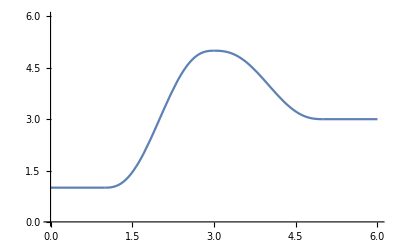

```mathematica
anim1[t_]:=EasyEase[t,{1,1} ,{3,5},{5,3}]; (*определение гладкой функции, проходящия через ключевые кадры {Subscript[t, 1],Subscript[x, 1]}={1,1},  {Subscript[t, 2],Subscript[x, 2]}={3,5} и {Subscript[t, 3],Subscript[x, 3]}={5,3}*)

Plot[anim1[t],{t,0,6},PlotRange->{0,6},LabelStyle->Directive[Larger]]
```

```mathematica
(*использование параметра в анимации*)
animrange1=6;
Dynamic[Plot[anim1[t],{t,0,6},PlotRange->{0,6},Epilog->{Red,InfiniteLine[{animrange1 t1,0},{0,1}]},PlotLabel-> "x="<>ToString[Round[anim1[animrange1 t1],.01]],AxesLabel->{"t","x"},LabelStyle->Directive[Larger]]]
Animator[Dynamic[t1]]
```

## Анимация функции

```mathematica
anim2[t_]:=EasyEase[t,
{0,x(3-x)},{1,x(3-x)},
{2,x+2Sin[2x]},{3,x+2Sin[2x]},
{4,2-x},{5,2-x},
{6,x(3-x)}
] (*гладкая интерполяция между функциями f(x)=x(3-x) при t∈[0,1], f(x)=x+2Sin[2x] при t∈[2,3] и f(x)=2-x при t∈[4,5]*)

(*анимация графика*)
animrange2=6;
Dynamic[
Plot[anim2[animrange2 t2],{x,0,3},PlotRange->{0,3},PlotStyle->Directive[Thickness[0.01],RGBColor[0.16, 0.51, 0.76]],AspectRatio->1,PlotLabel-> "t="<>ToString[Round[animrange2 t2,.01]],AxesLabel->{"x","f(x)"},LabelStyle->Directive[Larger]]
]
Animator[Dynamic[t2]]
```

## Анимация цветов

```mathematica
anim3[t_]:=EasyEase[t,{0,RGBColor[0.16, 0.63, 0.89]},{1,RGBColor[1, 0.2, 0.44]},{2,RGBColor[0.37, 0.8300000000000001, 0.12]},{3,RGBColor[0.16, 0.63, 0.89]}] (*гладкая интерполяция между функциями цветами RGBColor[0.16, 0.63, 0.89] RGBColor[1, 0.2, 0.44] RGBColor[0.37, 0.8300000000000001, 0.12]*)

animrange3=3;
Dynamic[
Graphics[{anim3[animrange3 t3],Disk[]}]
]
Animator[Dynamic[t3]]
```

## Комбинирование методов

```mathematica
animrange4=6;
f4[t_]=EasyEase[animrange4 t,{0,x(3-x)},{1,x+2Sin[2x]},{2,x+2Sin[2x]},{3,2-x},{4,2-x},{5,x(3-x)}]; (*анимированная функция*)
c4[t_]=EasyEase[animrange4 t,{0,RGBColor[0.16, 0.63, 0.89]},{1,RGBColor[1, 0.2, 0.44]},{2,RGBColor[1, 0.2, 0.44]},{3,RGBColor[0.37, 0.8300000000000001, 0.12]},{4,RGBColor[0.37, 0.8300000000000001, 0.12]},{5,RGBColor[0.16, 0.63, 0.89]}]; (*анимированный цвет*)

Pic[t_]:=Plot[f4[t],{x,0,3},PlotRange->{0,3.07},PlotStyle->Directive[AbsoluteThickness[4],c4[t]],AspectRatio->1
,Background->Lighter[Black, 0.2],AxesStyle->Directive[AbsoluteThickness[1],White],TicksStyle->AbsoluteThickness[1],LabelStyle->Directive[Larger],ImagePadding->{{35,45},{35,45}},AxesLabel->{"x","y"}
];

Dynamic[Pic[t4]]
Animator[Dynamic[t4]]
```

# Иллюстрации функций

В отличие от кривых Безье AnimationSegment задаёт явную завимимость анимируемого объекта от времени
Сравнение формы AnimationSegment и стандартной кривой Безье:

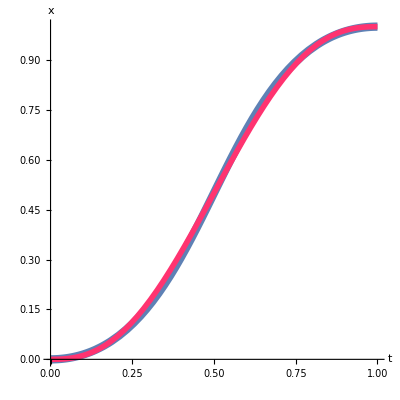

```mathematica
Show[{ParametricPlot[{0,0} t^3+3 {.5,0} t^2 (1-t)+3 {.5,1} t (1-t)^2+{1,1} (1-t)^3,{t,0,1},PlotStyle->Thickness[.015]],Plot[AnimationSegment[x],{x,0,1},PlotStyle->Directive[RGBColor[1, 0.2, 0.44],Thickness[.01]]]},AxesLabel->{"t","x"},LabelStyle->Directive[Larger]]
```

EasyEase[времяанимации_, ключевойкадр1_, ключевойкадр2_, ...] собирает сплайн из множества AnimationSegment, проходящий через заданные точки в заданные моменты времени
ключевойкадр = {момент времени, значение анимируемого параметра}
За пределами заданного набора анимируемый параметр имеет постоянные значения:

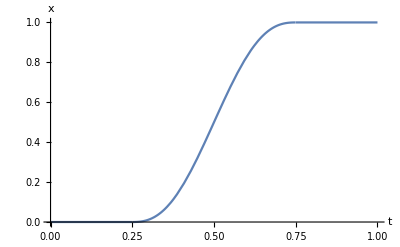

```mathematica
Plot[EasyEase[t,{.25,0},{.75,1}],{t,0,1},AxesLabel->{"t","x"},LabelStyle->Directive[Larger]]
```

Сравнение плавной интерполяции EasyEase и линейной интерполяции:

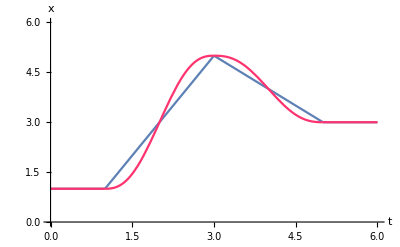

```mathematica
Plot[{
Linear[t,{1,1} ,{3,5},{5,3}],
EasyEase[t,{1,1} ,{3,5},{5,3}]
},{t,0,6},PlotRange->{0,6},AxesLabel->{"t","x"},LabelStyle->Directive[Larger],PlotStyle->{Automatic,RGBColor[1, 0.2, 0.44]}]
```

EasyEase имеет дополнительный скрытый параметр α, определяющий степень плавности анимации.
Значение α может быть задано последжним аргументом функции ([времяанимации_, ключевойкадр1_, ключевойкадр2_, ..., α_]). Если α явно не указан, его значение равно 1.5.
Сравнение кривых для различных значений α от -0.5 до 1.5:

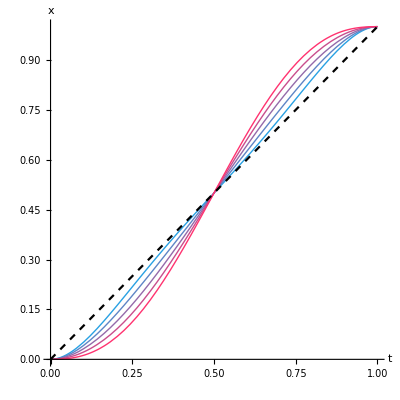

```mathematica
Plot[{
{Evaluate[EasyEase[t,{0,0} ,{1,1},#]&/@Subdivide[-.5,1.5,4]],
Linear[t,{0,0} ,{1,1}]}
},{t,0,1},AspectRatio->1,AxesLabel->{"t","x"},LabelStyle->Directive[Larger],PlotStyle->Append[Directive[Blend[{RGBColor[0.16, 0.63, 0.89],RGBColor[1, 0.2, 0.44]},#],Thick]&/@Subdivide[0,1,4],Directive[Dashed,Black]]]
```